# 9.2 Hmwk - Linear Regression &amp; Coeffic of Deter (Homework)

```mathematica
√0.962
```

0.980816

## Economics

```mathematica
data={{17,2},{34,4},{52,7},{28,5},{50,9},{25,3}};
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[-0.888701+0.171516 x]

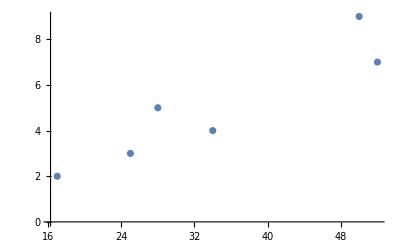

```mathematica
ListPlot[lm["Data"]]
```

```mathematica
lm["RSquared"]
```

0.852533

```mathematica
Total@lm["Data"][[All,1]]
```

206

```mathematica
Total@lm["Data"][[All,2]]
```

30

```mathematica
Total[#^2&/@lm["Data"][[All,1]]]
```

8058

```mathematica
Total[#^2&/@lm["Data"][[All,2]]]
```

184

```mathematica
Total[First[#]Last[#]&/@lm["Data"]]
```

1199

```mathematica
lm["RSquared"]
```

0.852533

```mathematica
√lm["RSquared"]
```

0.923327

```mathematica
Total@lm["Data"][[All,1]]/Length[lm["Data"]]//N
```

34.3333

```mathematica
Total@lm["Data"][[All,2]]/Length[lm["Data"]]//N
```

5.

```mathematica
lm["Function"][x]
```

-0.888701+0.171516 x

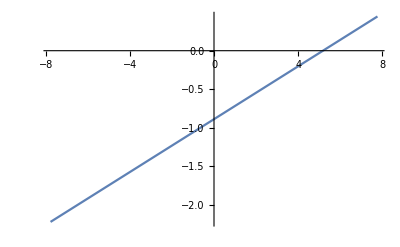

```mathematica
Plot[-0.8887009472259804+0.17151556156968875 x,{x,-7.772189349112421,7.772189349112421}]
```

```mathematica
lm["RSquared"]
```

0.852533

```mathematica
1-lm["RSquared"]
```

0.147467

```mathematica
lm["Function"][45]
```

6.8295

## Cattle Ranch

You are the foreman of the Bar-S cattle ranch in Colorado. A neighboring ranch has calves for sale, and you are going to buy some calves to add to the Bar-S herd. How much should a healthy calf weigh? Let x be the age of the calf (in weeks), and let y be the weight of the calf (in kilograms).

```mathematica
data={{1,44},{5,45},{8,72},{16,100},{26,150},{36,200}};
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[31.2561+4.60287 x]

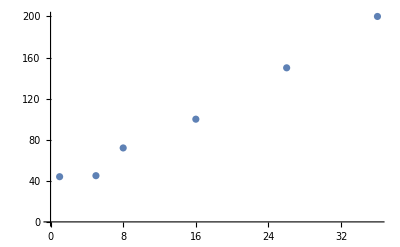

```mathematica
ListPlot[lm["Data"]]
```

```mathematica
92./Length[lm["Data"]]
```

15.3333

```mathematica
611./Length[lm["Data"]]
```

101.833

```mathematica
lm["Function"][x]
```

31.2561+4.60287 x

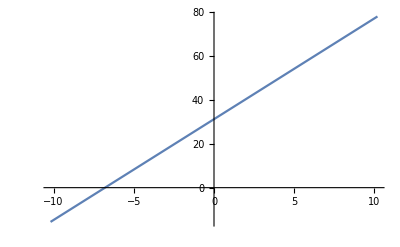

```mathematica
Plot[31.25606171932404+4.6028655400440845 x,{x,-10.185848830712754,10.185848830712754}]
```

```mathematica
lm["RSquared"]
```

0.989615

```mathematica
1-0.9896147088557146
```

0.0103853

```mathematica
lm["Function"][24]
```

141.725

## Automobile Driver ages and fatal accidents

Let x be the age in years of a licensed automobile driver. Let y be the percentage of all fatal accidents (for a given age) due to speeding. For example, the first data pair indicates that 35% of all fatal accidents of 17-year-olds are due to speeding

```mathematica
data={{17,35},{27,25},{37,21},{47,12},{57,10},{67,7},{77,5}};
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[39.425-0.489286 x]

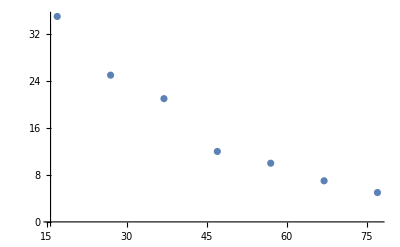

```mathematica
ListPlot[lm["Data"]]
```

```mathematica
Length[data]
```

7

```mathematica
329./7
```

47.

```mathematica
115/7.
```

16.4286

```mathematica
lm["Function"][x]
```

39.425-0.489286 x

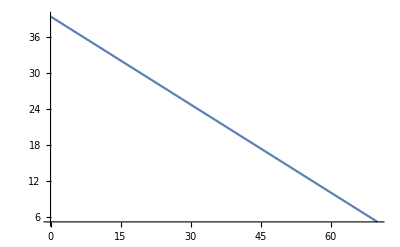

```mathematica
Plot[39.425000000000004-0.4892857142857144 x,{x,0,70}]
```

```mathematica
lm["RSquared"]
```

0.931372

```mathematica
100(1-lm["RSquared"])
```

6.86284

```mathematica
lm["Function"][35]
```

22.3

```mathematica
data={{2,4},{3,3},{6,7}};
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[1.42308+0.884615 x]

```mathematica
lm["Function"][x]
```

1.42308+0.884615 x

```mathematica
data={{4,2},{3,3},{7,6}};
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[-0.461538+0.884615 x]

```mathematica
lm["Function"][x]
```

-0.461538+0.884615 x

```mathematica
data={{2,4},{3,3},{6,7}};
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[1.42308+0.884615 x]

```mathematica
First[SolveValues[lm["Function"][x]==y,x]]//Expand
```

-1.6087+1.13043 y

## Basketball Fouls

```mathematica
data={{1,51},{2,42},{5,33},{6,26}};
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[53.6471-4.47059 x]

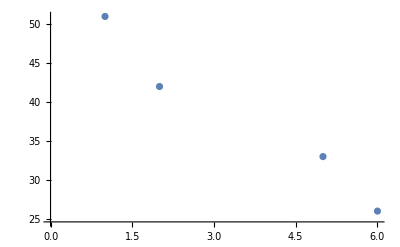

```mathematica
ListPlot[lm["Data"]]
```

```mathematica
sumX=Total[lm["Data"][[All,1]]]
```

14

```mathematica
sumY=Total[lm["Data"][[All,2]]]
```

152

```mathematica
sumXSquared=Total[#^2&/@lm["Data"][[All,1]]]
```

66

```mathematica
sumYSquared=Total[#^2&/@lm["Data"][[All,2]]]
```

6130

```mathematica
sumXY=Total[First[#]Last[#]&/@lm["Data"]]
```

456

```mathematica
√lm["RSquared"]
```

0.979687

```mathematica
lm["Function"][x]
```

53.6471-4.47059 x

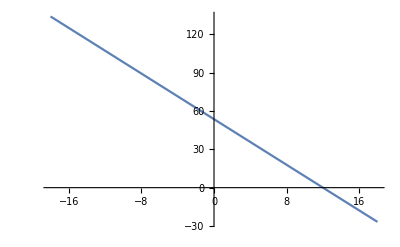

```mathematica
Plot[53.64705882352943-4.47058823529412 x,{x,-17.999999999999993,17.999999999999993}]
```

```mathematica
lm["RSquared"]
```

0.959787

```mathematica
100lm["RSquared"]
```

95.9787

```mathematica
100-100lm["RSquared"]
```

4.02127

```mathematica
lm["Function"][3]
```

40.2353

## Baseball

```mathematica
data={{0.239,1.0},{0.257,3.3},{0.286,5.5},{0.263,3.8},{0.268,3.5},{0.339,7.3},{0.299,5.0}};
```

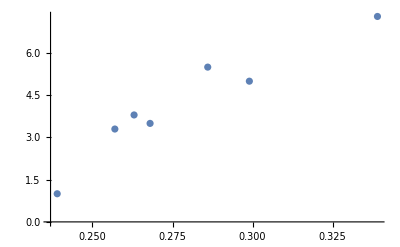

```mathematica
ListPlot[data]
```

```mathematica
lm=LinearModelFit[data,x,x]
```

FittedModel[-11.7707+57.3015 x]

```mathematica
√lm["RSquared"]
```

0.950854

## Binomial Hypothesis

```mathematica
Probability[x>1,x\[Distributed]BinomialDistribution[10,0.5]]
```

0.989258

```mathematica
Probability[x>1,x\[Distributed]BinomialDistribution[52,0.77]]
```

1.

```mathematica
NProbability[x>1,x\[Distributed]BinomialDistribution[52,0.77]]
```

```mathematica
NProbability[p<0.77,p\[Distributed]NormalDistribution[]]
```

## Normal Approximation to Binomial Distribution

The U.S. Department of Transportation, National Highway Traffic Safety Administration, reported that 77% of all fatally injured automobile drivers were intoxicated. A random sample of 52 records of automobile driver fatalities in a certain county showed that 35 involved an intoxicated driver. Do these data indicate that the population proportion of driver fatalities related to alcohol is less than 77% in Kit Carson County? Use 𝛼 = 0.10.

The sample sample is 52,

```mathematica
nSampleSize=52.;
Successes=35.;
```

```mathematica
probabilitySuccess=Successes/nSampleSize
```

0.673077

```mathematica
probabilityFailure=1-probabilitySuccess
```

0.326923

Check if we can apply the normal approximation to the binomial:

```mathematica
nSampleSize probabilitySuccess>5
```

True

```mathematica
nSampleSize probabilityFailure>5
```

True

```mathematica
meanMu=nSampleSize probabilitySuccess
```

35.

```mathematica
variance=nSampleSize probabilityFailure probabilitySuccess
```

11.4423

```mathematica
standardDeviation=√variance
```

3.38265

```mathematica
0.77 52
```

40.04

```mathematica
NProbability[x<-1.23315,x\[Distributed]NormalDistribution[]]
```

0.10876

## Weighted Averages

```mathematica
{0.21,0.245,0.245,0.30}.{96,84,84,66}
```

81.12

## Basketball Check work

```mathematica
basketballData={{1,51},{2,42},{5,33},{6,26}};
```

```mathematica
ListPlot[basketballData]
```

-Graphics-

```mathematica
Total[basketballData[[All,1]]]
```

14

```mathematica
Total[basketballData[[All,2]]]
```

152

```mathematica
Total[#^2&/@basketballData[[All,1]]]
```

66

```mathematica
Total[#^2&/@basketballData[[All,2]]]
```

6130

```mathematica
Total[First[#]Last[#]&/@basketballData]
```

456

```mathematica
basketballFit=LinearModelFit[basketballData,x,x]
```

FittedModel[53.6471-4.47059 x]

```mathematica
basketballFit["RSquared"]
```

0.959787

```mathematica
√basketballFit["RSquared"]
```

0.979687

```mathematica
basketballFit["Function"][x]
```

53.6471-4.47059 x

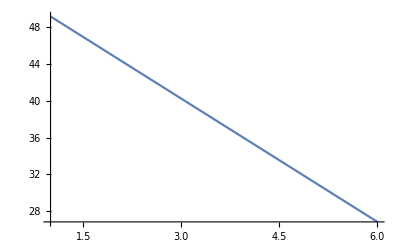

```mathematica
Plot[53.64705882352943-4.47058823529412 x,{x,1,6}]
```

```mathematica
basketballFit["RSquared"]
```

0.959787

```mathematica
100(1-basketballFit["RSquared"])
```

4.02127

```mathematica
basketballFit["Function"][3]
```

40.2353

## Baseball Check

```mathematica
baseballData={{0.239,1.0},{0.257,3.3},{0.286,5.5},{0.263,3.8},{0.268,3.5},{0.339,7.3},{0.299,5.0}};
```

```mathematica
ListPlot[{{0.239,1.},{0.257,3.3},{0.286,5.5},{0.263,3.8},{0.268,3.5},{0.339,7.3},{0.299,5.}}]
```

-Graphics-

```mathematica
baseballFit=LinearModelFit[baseballData,x,x]
```

FittedModel[-11.7707+57.3015 x]

```mathematica
baseballFit["RSquared"]
```

0.904123

```mathematica
√baseballFit["RSquared"]
```

0.950854

## Chapter 6 Discussion Forum

```mathematica
ClearAll[z]
```

```mathematica
NProbability[z<#,z\[Distributed]NormalDistribution[]]&[-1.2]
```

0.11507

```mathematica
NProbability[z>#,z\[Distributed]NormalDistribution[]]&[-1.2]
```

0.88493

```mathematica
NProbability[z>#,z\[Distributed]NormalDistribution[]]&[-0.25]
```

0.598706

```mathematica
ⅇ^6//N
```

403.429